# Analysis of Packing V3E05L1N01T3_1

Three Vertices, Five Edges, 1 Loop,Combinatorial Number 01, Face Pattern 3, Type 1

```mathematica
-Graphics-;
```

Note that (x2a,y2a) represents the center of smaller (with radius rs) circle  2, and (x3a, y3a) represents the center of smaller  (with radius rs) circle 3.

We use the property that the center of 2 is on the perpendicular bisector of w2 and the center of 3 is on the perpendicular bisector of w1+w2.

```mathematica
y2a:=((L/2)*Sin[θ]-(1/Tan[θ])(x2a-(L/2)*Cos[θ]))
```

```mathematica
y3a:=((L/2)*Sin[θ]-(1/Tan[θ])(x3a-((L/2)*Cos[θ]+1)))
```

Also, since we have a self tangency we need rb=1/2.  So, the following equations guarantee our edge lengths, as well as the tangency between the two small circles.

```mathematica
eq6a:={x2a^2+y2a^2==(1/Sqrt[2])^2, (x3a-x2a)^2+(y3a-y2a)^2==(Sqrt[2]-1)^2,(x3a-1)^2+(y3a)^2==(1/Sqrt[2])^2};
```

```mathematica
sol6a:=Simplify[Solve[eq6a,{x2a,x3a,L}]]
```

```mathematica
Simplify[sol6a]
```

{{x2a→1/4 (1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ])))-2 Cos[θ] √(-1+2 √2-√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))+Cos[2 θ] (1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))),x3a→1/4 (3-√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))+Cos[2 θ] (1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ])))-2 Cos[θ] √(-1+2 √2-√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))+Cos[2 θ] (1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))),L→-√(-1+2 √2-√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))+Cos[2 θ] (1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))},{x2a→1/4 (1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ])))+2 Cos[θ] √(-1+2 √2-√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))+Cos[2 θ] (1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))),x3a→1/4 (3-√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))+Cos[2 θ] (1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ])))+2 Cos[θ] √(-1+2 √2-√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))+Cos[2 θ] (1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))),L→√(-1+2 √2-√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))+Cos[2 θ] (1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))},{x2a→1/4 (1-√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))+Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ])))-2 Cos[θ] √(-1+2 √2+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))),x3a→1/4 (3+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ])))-2 Cos[θ] √(-1+2 √2+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))),L→-√(-1+2 √2+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))},{x2a→1/4 (1-√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))+Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ])))+2 Cos[θ] √(-1+2 √2+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))),x3a→1/4 (3+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ])))+2 Cos[θ] √(-1+2 √2+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))),L→√(-1+2 √2+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))}}

```mathematica
N[sol6a/.{θ->Pi/2}]
```

{{x2a→0.707107,x3a→0.292893,L→-2.58096×10^-8},{x2a→0.707107,x3a→0.292893,L→2.58096×10^-8},{x2a→0.292893,x3a→0.707107,L→-1.28719},{x2a→0.292893,x3a→0.707107,L→1.28719}}

We know that there is a solution on the rectangle, i.e. when θ = Pi/2.

Indicates the last solution is the correct corresponding to the circle centers since both are positive.

```mathematica
Simplify[(√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))))]
```

√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))

Now we substitute in for this value of L.

```mathematica
yep2:={x2a->1/4 (1-√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))+Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ])))+2 Cos[θ] √(-1+2 √2+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ])))))}
```

```mathematica
yep3:={x3a->1/4 (3+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ])))+2 Cos[θ] √(-1+2 √2+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ])))))}
```

```mathematica
Simplify[y2a/.yep2]
```

1/2 (L Sin[θ]+Cos[θ] ((L-√(-1+2 √2+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))) Cot[θ]+(-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))) Sin[θ]))

```mathematica
Simplify[y3a/.yep3]
```

1/2 L Sin[θ]-1/2 Cos[θ] ((-L+√(-1+2 √2+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))-Cos[2 θ] (-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))))) Cot[θ]+(-1+√((-5+4 √2+Cos[2 θ])/(-1+Cos[2 θ]))) Sin[θ])

Thus, now we have our circle centers.

## Circle Centers and Radii

KEY
β = θ
α = L

```mathematica
centers = Simplify[{{0,0},

{1/4 (1-√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))+Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))+2 Cos[β] √(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))),1/2 ((√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))) Sin[β]+Cos[β] (((√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))))-√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))) Cot[β]+(-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))) Sin[β]))},{1/4 (3+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))+2 Cos[β] √(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))),1/2 (√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))) Sin[β]-1/2 Cos[β] ((-(√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))))+√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))) Cot[β]+(-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))) Sin[β])}




}]
```

{{0,0},{1/4 (1-√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))+Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))+2 Cos[β] √(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))),1/2 (Cos[β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))+√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))) Sin[β]},{1/4 (3+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))+2 Cos[β] √(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))),1/2 (Cos[β]-Cos[β] √((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))+√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))) Sin[β]}}

## Lattice Vectors

We are working this flat torus

```mathematica
latticeVectors = Simplify[{
 {1,0},
{ (√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))))*Cos[β],(√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))))*Sin[β]}}];
```

## Edges

Here we store the edges a list {i,j,m,n} where center[[i]] is connected to center[[j]] + m*latticeVectors[[1]] + n*latticeVectors[2]]
center[[i]] is *always* in the fundamental domain ****the last two numbers are winding numbers****

```mathematica
edges = {{1,2,0,0},{1,1,1,0},{2,3,0,0},{2,1,0,1},{3,1,1,0},{3,1,1,1}};
```

### Check the edge lengths are all 2rs= Sqrt[2]-1 or rs+rb=Sqrt[2]rb=Sqrt[2]/2=1/Sqrt[2]

```mathematica
For[i=1,i≤Length[edges],i++,
P1:= centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]];
P2:= centers[[edges[[i,1]] ]];
Print["Edge ",i,": Length is ",
Sqrt[FullSimplify[(P1[[1]]-P2[[1]])^2+(P1[[2]]-P2[[2]])^2,{Pi/3≤β≤Pi/2}]]];
]
```

Edge 1: Length is 1/(√2)

Edge 2: Length is 1

Edge 3: Length is √(3-2 √2)

Edge 4: Length is 1/(√2)

Edge 5: Length is 1/(√2)

Edge 6: Length is 1/(√2)

Yes!

## Packing Visualization

Here we visualize the packing and the fundamental domain to help determine the value of the parameters for which this is a packing graph.

```mathematica
Animate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}}(*Angle Markers Labels*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{b,Pi/2,"β"},1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]),Pi/2},AnimationRunning -> False
]
```

## Locally Maximally Dense

We have to determine for which values of α and β the packing is locally maximally dense. To be locally maximally dense (Following Connelly, Rigid Circle and Sphere Packings, Page 51, Theorem 6.1)
	1. The packing graph is rigid as a bar framework
	2. Have a proper stress that is non-zero on every member

### Rigid as bar framework

To be rigid as a bar framework we need to establish a rigid ordering of the circles. The numbering of the circles in the picture above is a rigid ordering of the packing disks -- See Lemma 6.2 in the Connelly paper on Rigid Sphere and Circle Packings. Note: The first is held fixed.

### Proper Stress

Assign a scalar to each edge of the packing and collect those scalars in a vector called ω. We need to solve the linear algebra problem where the sum of the ω_i times the vector from vertex j is zero.

```mathematica
Animate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}},(*Angle Markers Labels*)
Table[Text[Style[Subscript["ω",i],Large,Red],1/2*(centers[[edges[[i,1]] ]]+centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]])/.{α->a,β->b}],{i,1,Length[edges]}](*Label Edges With Stresses*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{b,Pi/2,"β"},1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]),Pi/2},AnimationRunning -> False
]
```

```mathematica
equations = Table[{0,0},{k,Length[centers]}]; (*Start with the zero equations*)
w =Table[Subscript[ω,i],{i,Length[edges]}]; (*Initialize a vector of Subscript[ω, i]*)
For[i=1,i≤Length[centers], i++, (*i is the center number*)
For[j=1,j≤Length[edges], j++, (*j is the edge number*)
If[edges[[j,1]]==i, (*center i is the starting point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(centers[[edges[[j,1]] ]]-centers[[edges[[j,2]] ]]-
edges[[j,3]]*latticeVectors[[1]]-
edges[[j,4]]*latticeVectors[[2]])] 
If[edges[[j,2]]==i, (*center i is the ending point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(-centers[[edges[[j,1]] ]]+centers[[edges[[j,2]] ]]+
edges[[j,3]]*latticeVectors[[1]]+
edges[[j,4]]*latticeVectors[[2]])]
]
]
stresses = Flatten[Simplify[Solve[Flatten[equations]==Flatten[Table[{0,0},{k,Length[centers]}]],w]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{ω_1→-(((Cos[β]-Cos[β] √((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])) √(-1+2 √2+Cos[2 β]+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] √((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))) ω_3)/((-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))) √(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))))),ω_4→-(((Cos[β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])) √(-1+2 √2+Cos[2 β]+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] √((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))) ω_3)/((-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))) √(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))))),ω_5→-(((Cos[β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])) √(-1+2 √2+Cos[2 β]+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] √((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))) ω_3)/((-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))) √(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))))),ω_6→-(((Cos[β]-Cos[β] √((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])) √(-1+2 √2+Cos[2 β]+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] √((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))) ω_3)/((-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))) √(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))))}

Notice that stress ω_1 is free.

```mathematica
yuck := Simplify[equations /. stresses] (*check the solutions, Should output all zeros but I don't think Mathematica can simplify it*)
```

```mathematica
N[Simplify[yuck/.{Subscript[ω, 3]-> 1,β-> Pi/2}]]
```

{{0.,0.},{0.,0.},{0.,0.}}

```mathematica
guts := Simplify[Union[{0},Table[Subscript[ω, i]/.stresses,(*first list all of the right hand sides of all the stresses*)
{i,Length[edges]}]/.Subscript[ω, 3]->1]]
```

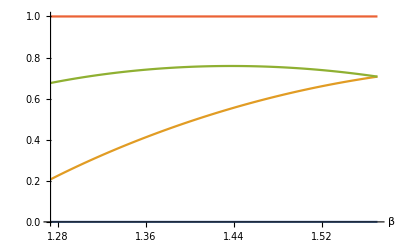

```mathematica
Plot[guts,{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]),Pi/2},RegionFunction->Function[{α,β},α>β],AxesLabel->Automatic]
```

Stresses are positive, lets gooooooooooooooo

## Moduli Space Of Locally Maximally Dense Packings

Determine the Torus Angle and Ratio for the packings that are locally maximally dense.

```mathematica
torusAngleFromVectors = FullSimplify[VectorAngle[latticeVectors[[1]],latticeVectors[[2]]],{Element[{β},Reals],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])≤β≤Pi/2}]
```

ArcCos[(Conjugate[√(-1+2 √2+Cos[2 β]+√((-1+Cos[2 β]) (-5+4 √2+Cos[2 β])))] Cos[β])/(√Abs[-1+2 √2+√(1-2 (-1+√2) Csc[β]^2)-Cos[2 β] (-1+√(1-2 (-1+√2) Csc[β]^2))])]

```mathematica
torusRatio = FullSimplify[EuclideanDistance[{0,0},latticeVectors[[2]]]/EuclideanDistance[{0,0},latticeVectors[[1]]],{Element[{β},Reals],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])≤β≤Pi/2}]
```

√Abs[-1+2 √2+√(1-2 (-1+√2) Csc[β]^2)-Cos[2 β] (-1+√(1-2 (-1+√2) Csc[β]^2))]

Now plot the region of the moduli space that is covered by (r,theta)=(torusRatio,torusAngle). The right boundary is in the region, the others are not.

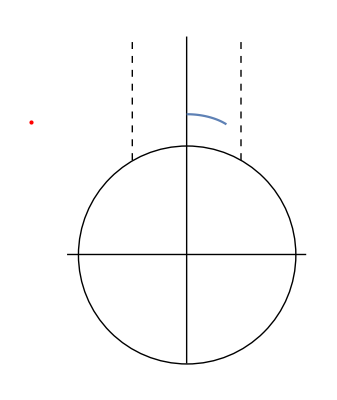

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]),Pi/2}],
(*Least dense globally maximally dense point*)
Graphics[{Red,Point[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]}/.{α->2.4907302,β->2.4907302}]}
]]
```

## Density Of Packings

Here we analyze the density of the locally maximally dense packings and explore the density.

```mathematica
torusDensity = FullSimplify[(Pi*(1/2)^2+2*Pi*(1/2(Sqrt[2]-1))^2)/(Norm[latticeVectors[[1]]]*Norm[latticeVectors[[2]]]*Sin[torusAngleFromVectors]) ,{Element[{β},Reals],1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])≤β≤Pi/2}]
```

((7-4 √2) π)/(4 √(Abs[-1+2 √2+√(1-2 (-1+√2) Csc[β]^2)-Cos[2 β] (-1+√(1-2 (-1+√2) Csc[β]^2))]-Conjugate[√(-1+2 √2+Cos[2 β]+√((-1+Cos[2 β]) (-5+4 √2+Cos[2 β])))]^2 Cos[β]^2))

Plot the density over the parameter space

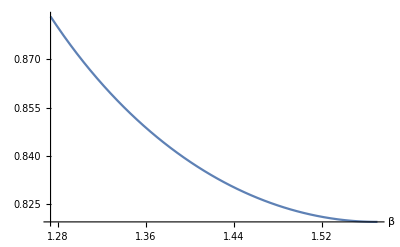

```mathematica
Plot[torusDensity,{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]),Pi/2},AxesLabel->Automatic]
```

Color the moduli space region with color depending on the density. Red shade is close to 1 and Blue shade is close to .5

```mathematica
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]),Pi/2},ColorFunction->(Hue[torusDensity]/.{α ->#3,β->#4} &),ColorFunctionScaling->False,BoundaryStyle->Directive[Black,Thick,Dashed],Mesh->None]
```

Infinity::indet: Indeterminate expression -1+2 √2+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

Now find the minimum and maximum density with in the region.

```mathematica
NMinimize[{torusDensity,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])< β && β < Pi/2 },{{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]),Pi/2}},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

{0.8195413498965238636536951994699096727628,{β→1.570796326794896619231321691639751442099}}

```mathematica
NMaximize[{torusDensity,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])< β && β < Pi/2 },{{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]),Pi/2}},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

{0.88331053808648840173050934060636024001,{β→1.273544965473689813278498648511408866756}}